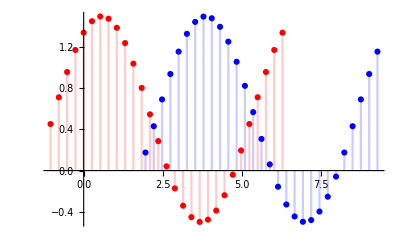

```mathematica
(*时移*)
Show[DiscretePlot[Sin[x+1]+0.5,{x,-π/3,2π,π/12},PlotStyle->Red],
	DiscretePlot[Sin[x+4]+0.5,{x,-π/3+3,3+2π,π/12},PlotStyle->Blue],
	PlotRange->All]
```

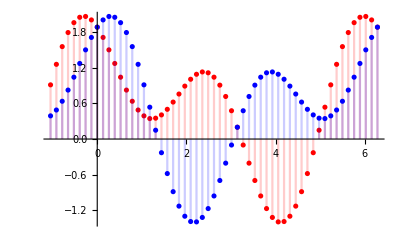

```mathematica
(*时间反转*)
Show[DiscretePlot[Sin[x+1]+Cos[2x+1]+0.5,{x,-π/3,2π,π/24},PlotStyle->Red],
	DiscretePlot[Sin[-x+1]+Cos[-2x+1]+0.5,{x,-π/3,2π,π/24},PlotStyle->Blue],
	PlotRange->All]
```

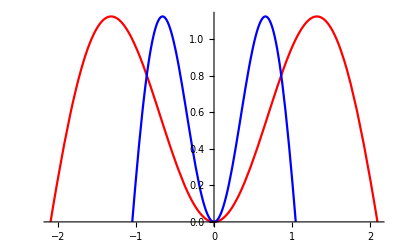

```mathematica
(*时间尺寸变换*)
Show[Plot[Sin[x+π/2]+Cos[2(x+π/2)],{x,(-2π)/3,2/3 π},PlotStyle->Red],
	Plot[Sin[2(x+π/4)]+Cos[4(x+π/4)],{x,-π/3,π/3},PlotStyle->Blue],
	PlotRange->All]
```

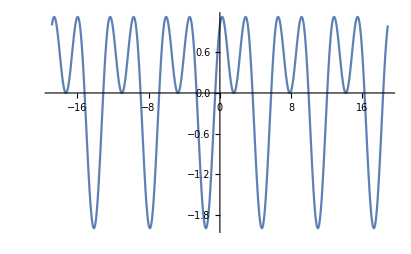

```mathematica
(*周期信号*)
Plot[Sin[x]+Cos[2x],{x,-6π,6π}]
```

```mathematica
(*奇偶信号*)
ClearAll;
f[x_]:=Sin[x]+Cos[2x];
Plot[{f[x],1/2(f[x]+f[-x]),1/2(f[x]-f[-x])},{x,-3,3},PlotStyle->{Purple,Blue,Red},PlotLabels->{原函数,偶部,奇部}]
```

-Graphics-

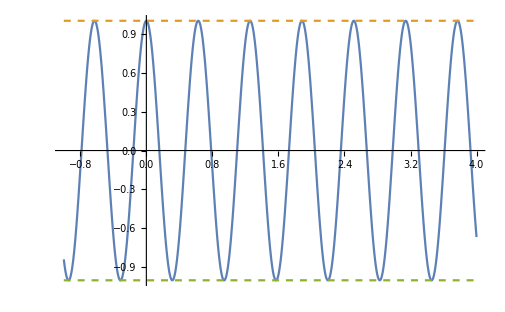

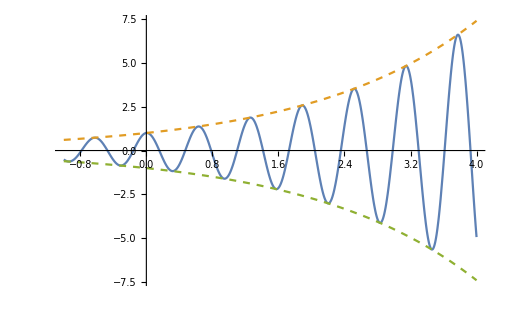

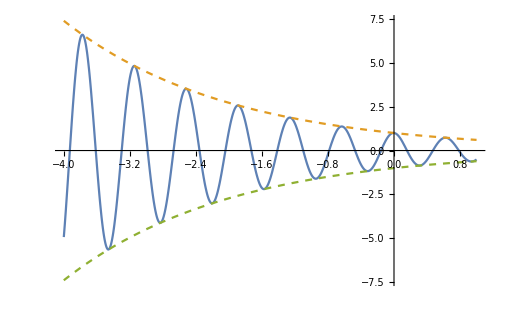

```mathematica
(*正弦信号&正弦衰减/增长信号*)
ClearAll;
θ=0;
f[t_,w_,c_,r_]:=Abs[c] ⅇ^(r t)Cos[w t+θ];
g[t_,w_,c_,r_]:=c ⅇ^(r t);
Plot[{f[t,10,1,0],g[t,10,1,0],g[t,10,-1,0]},{t,-1,4},PlotRange->All,PlotStyle->{,Dashed,Dashed}]
Plot[{f[t,10,1,0.5],g[t,10,1,0.5],g[t,10,-1,0.5]},{t,-1,4},PlotRange->All,PlotStyle->{,Dashed,Dashed}]
Plot[{f[t,10,1,-0.5],g[t,10,1,-0.5],g[t,10,-1,-0.5]},{t,-4,1},PlotRange->All,PlotStyle->{,Dashed,Dashed}]
```

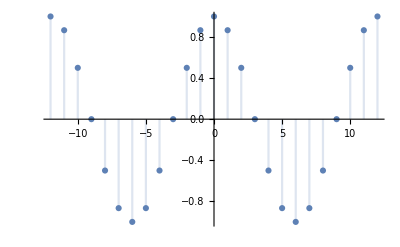

```mathematica
ClearAll;
DiscretePlot[Cos[(π n)/6],{n,-12,12}]
```

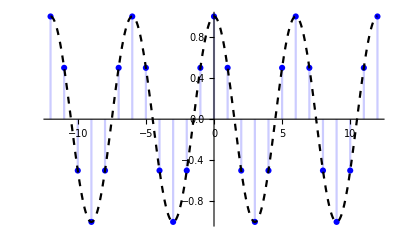
-Graphics-cos(π/3n)

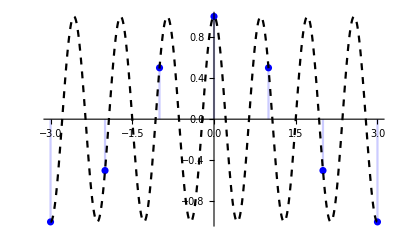
-Graphics-cos((7  π)/3n)

```mathematica
(*离散时间复指数周期不变性*)
Labeled[Show[DiscretePlot[Cos[(π n)/3],{n,-12,12},PlotStyle->Blue],Plot[Cos[(π x)/3],{x,-12,12},PlotStyle->{Dashed,Black}]],"cos(π/3n)"]
Labeled[Show[DiscretePlot[Cos[(7π n)/3],{n,-3,3},PlotStyle->Blue],Plot[Cos[(7π x)/3],{x,-3,3},PlotStyle->{Dashed,Black}]],"cos((7  π)/3n)"]
```

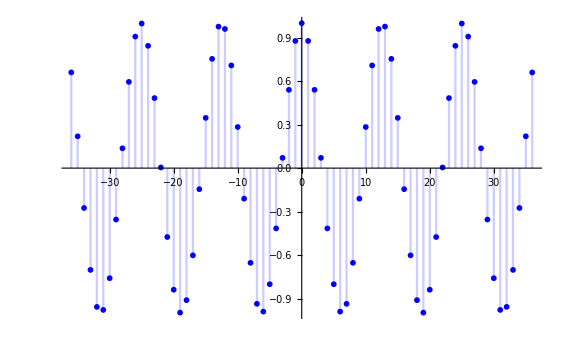

```mathematica
(*离散连续复指数无理数非周期性*)
DiscretePlot[Cos[n/2],{n,-36,36},PlotStyle->Blue]
```

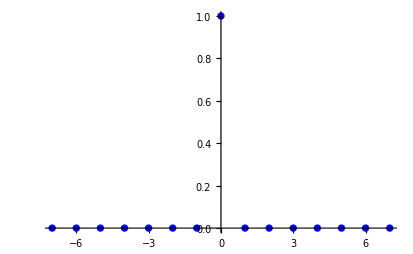

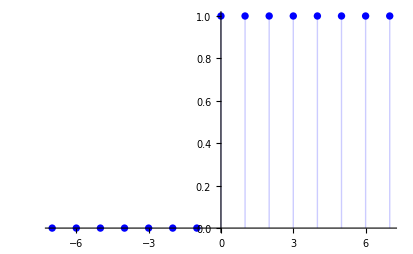

```mathematica
(*离散单位脉冲&单位阶跃*)
DiscretePlot[Piecewise[{{0,n!=0},{1,n==0}}],{n,-7,7},PlotStyle->{Thick,Blue}]
DiscretePlot[HeavisideTheta[n+0.1],{n,-7,7},PlotStyle->{Thick,Blue}]
```

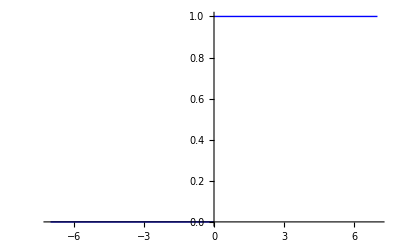

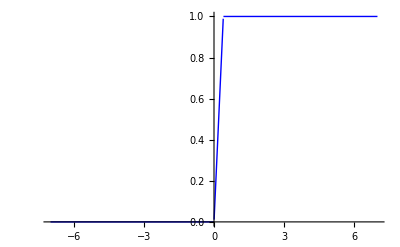

```mathematica
(*连续单位阶跃*)
ClearAll;
Plot[HeavisideTheta[x],{x,-7,7},PlotStyle->{Thick,Blue}]
Plot[Piecewise[{{0,x<0},{2.5x,0≤ x≤ 0.4},{1,x>0.4}}],{x,-7,7},PlotStyle->{Thick,Blue}]
```

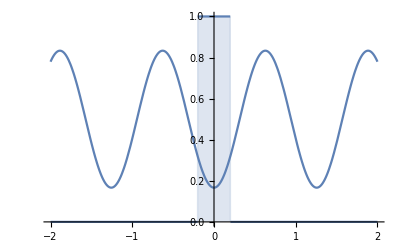

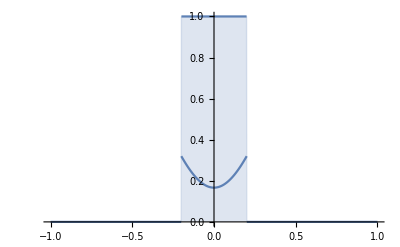

```mathematica
(*单位冲激采样*)
ClearAll;
f[x_]:=1/3(-Cos[5x]+1.5);
Show[Plot[Piecewise[{{0,x<-0.2},{1,-0.2≤ x≤ 0.2},{0,x>0.1}}],{x,-2,2},Filling->Axis],Plot[f[x],{x,-2,2}]]
Show[Plot[Piecewise[{{0,x<-0.2},{1,-0.2≤ x≤ 0.2},{0,x>0.1}}],{x,-1,1},Filling->Axis],Plot[f[x],{x,-0.2,0.2}]]
```